```mathematica
(* taken from wolfram demos for binomial confidence intervals: http://demonstrations.wolfram.com/ConfidenceIntervalsForTheBinomialDistribution *)
```

```mathematica
(* j is successes, n is trials (attempts, samples ), p is probably the confidence? *) 
b[j_,n_,p_]:=CDF[BinomialDistribution[n,p],j];
intervals[jj_,nn_,confLvl_, opts___]:=Module[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2],
blueSquare=Graphics[{Blue,Rectangle[]},ImageSize->10],redSquare=Graphics[{Red,Rectangle[]},ImageSize->10],blackSquare=Graphics[{Black,Rectangle[]},ImageSize->10],izq,der,interWald,interWilson,nums,int1,int2,int3,std,corrnums,stimes},
izq=Quiet@If[jj==1,0,(p/.NSolve[1-b[jj-1,nn,p]==(1-confLvl)/2,p])[[1]]];der=Quiet@(p/.NSolve[b[jj,nn,p]==(1-confLvl)/2,p])[[1]];
interWald=Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)};
interWilson={1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))};int1=interWald;
int2=interWilson;
int3={izq,der};nums={interWald,interWilson,{izq,der}};
std=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@Flatten[nums]));difs=#[[2]]-#[[1]]&/@nums;
az=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@difs));
corrnums=Table["["<>std[[j]]<>","<>" "<>std[[j+1]]<>"]",{j,1,Length[std]-1,2}];stimes=Text[#]&/@Table[corrnums[[j]]<>"      "<>az[[j]],{j,1,3}];
ListLinePlot[{{jj/nn,0},{jj/nn,0.003}},Axes->{True,False},AxesOrigin->{0.25,0},PlotStyle->{Black,Thickness[0.001]},PlotRange->{{0,1},{-0.002,0.009}},Epilog->{Text[Style["j/n",Italic,Medium],{jj/nn,-0.00075}],Inset[Grid[{{Style[StringJoin[ToString[confLvl*100],"% confidence intervals"],Medium]},{Style["for the probability parameter",Medium]},{Style["in a binomial distribution",Medium]}}],{0.5,0.008}],Inset[Grid[{{Text["method"],Text[""],Text["  interval           length"]},{Text["conventional"],blueSquare,stimes[[1]]},{Text["Wilson"],redSquare,stimes[[2]]},{Text["Clopper-Pearson"],blackSquare,stimes[[3]]}}],{0.5,0.005}],Thick,Blue,Line@MapThread[List,{int1,{0.003,0.003}}],Thick,Red,Line@MapThread[List,{int2,{0.002,0.002}}],Thick,Black,Line@MapThread[List,{int3,{0.001,0.001}}]},opts]]
```

```mathematica
Manipulate[
If[successes>tries-2,successes=tries-2];
intervals[successes,tries,confidence, ImageSize->550],
{{successes,10},1,tries-2,1,Appearance->"Labeled"},
{{tries,50},20,200,5,Appearance->"Labeled"},{{confidence,0.95},0.5,0.99,0.01,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
(* redefining Wald CI for convenience *) 
interWald[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]},Interval[Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)}]];
```

```mathematica
(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]]
```

```mathematica
(*** FILE MANIPULATIONS ***)
dataDirPath = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";

monFilenames[winSize_, idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@idpairlist;

allMonFilenames[winSize_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

detFilenames[idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@idpairlist;

allDetFilenames = StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(* various counts from mons, for sanity *) 
allMonH1ct = countFromFiles[ "h1count",allMonFilenames[10]]
allMonFNct = countFromFiles[ "FNcount",allMonFilenames[10]]
allDetH0ct =countFromFiles[ "h0count",allDetFilenames]
allDetFPct =countFromFiles[ "FPcount",allDetFilenames]
```

580

389

1000

110

```mathematica
(* PREDICTIONS basics *) 
predFNR[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);

chart95conf = ListLinePlot[Inner[List, Range[0,24],Table[0.95, 25], List], PlotStyle->{Red, Dotted}];(*ListLinePlot[Table[0.95, 25], PlotStyle->{Red, Dotted}];*)
```

```mathematica
subsetCt = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1]] - 1;
subsetCt23to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25}];
subsetCt20to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25}];
```

```mathematica
(* COMPARISON: monitor FNR prediction vs data-driven CI *)
```

```mathematica
(* basic pairing for predicted monitor FNR, used in above *)
pairingPredMonFNR[pairIdList_, intervalType_] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10]};
```

```mathematica
(* generates a true/false response for intervals containing things in pairs, for a particular pairing function *) 
oneIntervalTestGeneral[pairingFn_,pairIdList_, intervalType_] := 
With[{testPair = pairingFn[pairIdList,intervalType]}, IntervalMemberQ[testPair[[1]], testPair[[2]]]];

(** randomized sampling, no constraints on subset size *) 

(* a list of pairs {subset size used, whether CI contains the prediciton}. Can do tripling if needed *) 
generateBinarySampleGeneral[pairingFn_, sampleCt_, intervalType_, testFn_:oneIntervalTestGeneral]:= ({#[[1]],oneIntervalTestGeneral[pairingFn, #[[2]], intervalType]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));

(* Represents trues and falses as counts, in triples of {subsetsize, # of trues at that size, # of falses at that size}.
Takes in a list of pairs {subset size, true/false} *)
tallyUpBinarySample[sample_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,25];

(* Evaluation of CI via random sampling of subset sizes, producing outcome pairs {subset size, accuracy w/uncert based on wilson CIs}, by converting tallied triples to ratios and stdev *) 
generateCIRSOutcomesGeneral[pairingFn_, sampleCt_, intervalTypeForEstim_, intervalTypeForEval_,testFn_:oneIntervalTestGeneral]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = intervalTypeForEval[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpBinarySample[generateBinarySampleGeneral[pairingFn, sampleCt, intervalTypeForEstim, testFn]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

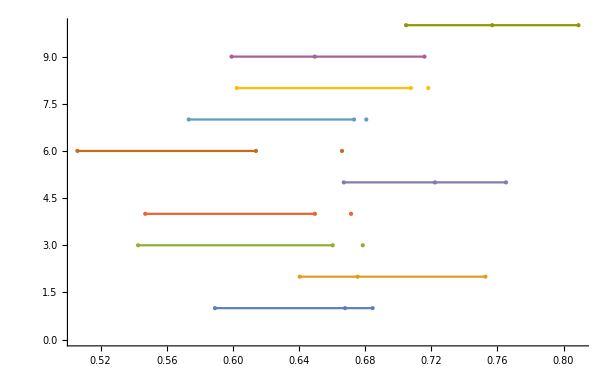

```mathematica
(*** VISUALS for PRED vs DATA-DRIVEN  ***) 

(* just a few samples *)
(* across all possible data -- poor performance *)
NumberLinePlot[pairingPredMonFNR[#, interWilson]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},10], PlotStyle->PointSize[Large]]
```

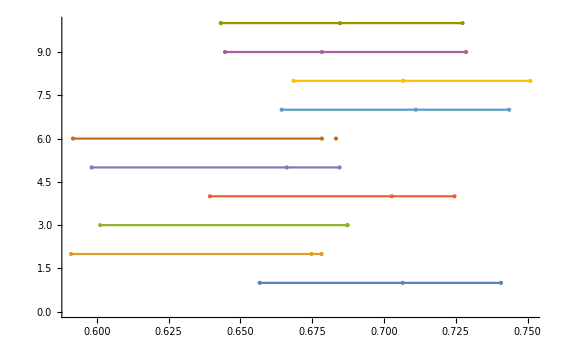

```mathematica
NumberLinePlot[pairingPredMonFNR[#, interWilson]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},10], PlotStyle->PointSize[Large]]
```

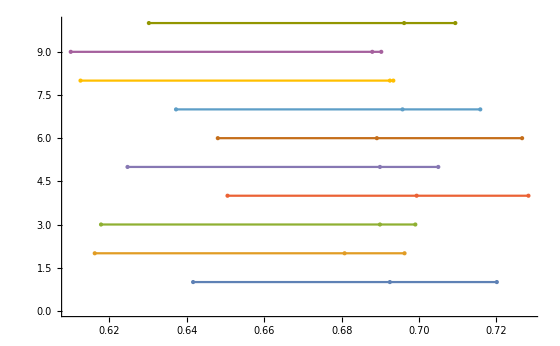

```mathematica
(* when substantial data is given -- good performance *)
NumberLinePlot[pairingPredMonFNR[#, interWilson]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},10], PlotStyle->PointSize[Large]]
```

```mathematica
(* sample success counts fixed per subset size *) 
generateSuccessCtsPerSubsetSize[pairingFn_, samplesPerSubsetSize_, intervalType_,testFn_:oneIntervalTestGeneral]  := With[{subsetsCt = #},
(* count truths *)Count[testFn[pairingFn, #, intervalType]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},samplesPerSubsetSize], {True}]
]& /@ Range[1, 24];

(* generates confidence intervals out of the above success counts *) 
generateCIOutcomesPerSubsetSize[pairingFn_, sampleCtPerSubsetSize_, intervalTypeForEstim_, intervalTypeForEval_,testFn_:oneIntervalTestGeneral]:= Inner[List, Range[1,24], #, List]& @(With[{est = #/ sampleCtPerSubsetSize, int = intervalTypeForEval[#, sampleCtPerSubsetSize, 0.95 ]}, Around[(*estimated accuracy*)est,(* converting interval to uncertainty bounds for charts*) {Min@int-est, Max@int-est}]] &/@generateSuccessCtsPerSubsetSize[pairingFn, sampleCtPerSubsetSize, intervalTypeForEstim,testFn] );
```

```mathematica
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCountsPerSubsetSize, 100]
```

```mathematica
reslists100 = {{73,77,67,80,75,74,82,78,83,72,86,77,74,81,83,79,83,92,89,87,93,94,99,100},{58,77,68,76,77,72,74,74,83,76,79,78,77,75,83,85,86,88,90,95,95,96,100,100},{68,74,67,67,66,78,68,84,76,85,77,80,77,81,83,75,87,83,93,92,96,98,99,100},{68,71,70,74,73,76,73,72,73,82,85,83,81,83,82,90,93,82,92,91,95,93,98,100},{68,78,77,78,77,68,78,73,65,75,81,82,79,80,88,79,84,89,89,88,93,95,99,100},{69,79,76,70,80,78,77,72,82,69,75,83,83,86,83,88,89,91,89,91,98,94,98,100},{71,77,73,77,74,72,74,68,82,81,82,87,83,80,92,78,85,87,91,92,96,95,99,100},{68,73,69,71,76,71,76,79,80,83,74,81,80,84,83,87,86,85,88,93,88,97,98,100},{65,82,70,73,76,69,75,78,75,86,81,82,78,79,83,84,89,88,95,88,92,97,98,100},{68,73,75,82,70,74,75,84,76,75,82,83,72,78,79,85,90,81,93,90,90,96,97,100},{69,68,65,75,80,80,72,75,78,74,71,77,80,86,81,84,86,86,90,91,92,96,98,100},{67,79,62,71,66,78,80,81,78,77,75,86,83,80,89,78,90,82,89,87,93,96,98,100},{65,75,65,70,81,74,77,77,72,78,82,77,88,85,88,87,82,87,91,95,92,92,98,100},{63,79,70,73,77,76,78,71,79,75,82,75,79,83,82,82,89,88,90,88,93,98,100,100},{73,76,69,75,72,66,78,76,78,69,83,75,75,81,76,88,87,85,88,87,90,96,99,100},{59,73,71,72,70,72,76,75,74,83,84,90,82,82,85,86,81,86,89,95,94,95,99,100},{68,78,73,78,75,81,69,82,81,82,81,80,83,83,87,83,84,89,90,95,92,96,99,100},{73,77,72,77,72,75,76,76,76,76,86,80,89,83,79,92,88,87,86,90,90,91,99,100},{62,73,73,66,69,75,75,74,76,83,80,79,80,85,82,84,89,93,87,91,91,95,97,100},{74,73,72,69,70,72,71,79,68,81,79,79,81,78,81,84,81,89,90,86,94,98,100,100},{65,78,70,80,75,83,77,77,73,81,86,74,90,84,92,84,86,88,93,90,91,97,99,100},{63,82,69,80,80,80,77,77,73,77,79,86,87,85,87,86,83,85,90,90,88,96,99,100},{68,70,65,76,79,74,68,79,76,79,74,80,84,79,82,89,83,90,87,92,93,95,100,100},{73,72,77,77,70,65,69,78,78,81,80,81,75,82,83,81,82,86,88,89,93,99,97,100},{72,78,75,70,72,80,68,75,79,75,81,82,86,83,85,84,94,84,91,93,91,96,98,100},{69,66,70,71,67,67,72,75,78,84,86,79,76,79,85,91,87,88,89,96,95,94,100,100},{72,68,71,75,66,71,75,75,72,74,83,84,83,82,81,84,82,88,91,87,94,97,100,100},{71,69,68,73,75,73,78,81,83,80,82,74,79,87,88,81,86,87,92,87,93,92,98,100},{72,74,63,70,72,77,71,71,76,83,79,82,86,86,84,82,82,87,85,95,93,97,100,100},{63,78,70,78,74,78,73,81,70,84,71,82,79,81,82,83,87,87,85,91,92,97,99,100},{68,77,72,75,79,70,77,78,79,79,76,79,81,84,90,85,85,88,89,92,84,98,100,100},{72,72,77,74,79,62,75,74,79,76,76,81,81,88,79,86,87,83,87,92,97,96,99,100},{67,73,72,70,78,71,67,75,79,78,81,82,83,82,83,86,85,87,88,83,92,97,98,100},{75,77,67,72,80,75,74,68,74,83,84,77,86,76,91,87,90,85,88,91,94,94,100,100},{67,77,71,76,76,71,77,80,80,79,84,79,83,83,77,83,83,89,85,90,94,95,100,100},{65,72,62,69,81,74,79,76,74,82,82,78,82,87,84,85,89,91,89,96,94,93,99,100},{70,79,71,71,75,76,68,74,74,86,79,77,80,86,82,86,87,86,95,92,92,96,99,100},{65,76,70,66,72,74,77,76,78,78,81,76,87,79,86,81,84,86,86,89,89,95,100,100},{59,77,70,64,69,76,67,83,71,79,82,79,80,84,82,81,87,89,85,90,94,95,98,100},{64,72,67,80,71,77,70,75,71,78,78,77,81,82,83,89,85,86,89,92,92,97,98,100},{61,68,68,74,65,80,69,73,75,77,71,81,74,76,83,81,78,85,93,91,95,94,99,100},{63,73,81,76,77,73,78,73,75,82,77,87,73,82,84,83,80,81,92,91,96,97,99,100},{65,65,71,72,69,68,74,82,86,80,70,84,86,76,86,83,88,82,92,88,94,96,99,100},{76,73,75,68,75,77,77,77,74,74,79,75,79,86,84,77,84,89,88,91,91,94,100,100},{67,71,72,73,73,78,74,76,79,86,74,79,81,76,78,77,93,87,89,90,87,90,97,100},{67,70,61,70,75,79,76,76,77,81,87,85,82,83,77,87,84,95,95,89,91,94,98,100},{66,68,74,76,78,77,71,72,79,85,80,86,83,83,84,87,90,87,90,91,96,95,99,100},{66,75,77,59,66,66,75,69,80,71,86,83,84,83,79,83,91,83,89,92,91,95,99,100},{65,74,74,74,69,74,71,75,75,81,84,75,85,85,79,86,88,89,90,91,90,98,100,100},{61,70,71,76,69,73,75,79,85,72,73,86,85,81,81,85,85,89,90,89,93,96,99,100},{78,75,70,70,74,85,82,78,72,74,74,77,83,80,74,87,84,88,90,87,93,98,99,100},{54,75,75,72,78,75,80,79,75,73,75,80,82,78,80,87,87,88,89,90,98,94,100,100},{76,74,71,71,70,76,81,74,81,74,79,77,86,82,85,87,90,90,91,89,95,93,98,100},{72,70,77,69,80,69,69,73,75,68,77,83,74,83,85,85,84,84,89,94,95,94,98,100},{72,62,80,77,74,83,82,80,76,83,72,82,82,86,82,83,84,86,84,85,99,95,99,100},{64,77,71,74,80,78,73,74,73,79,78,82,83,80,86,83,89,84,90,89,94,97,100,100},{69,74,75,65,72,74,72,71,77,67,79,82,78,82,87,87,89,85,90,91,99,99,100,100},{77,68,70,72,76,66,79,78,77,73,76,84,83,67,82,83,86,83,87,92,97,95,99,100},{71,76,74,70,73,80,73,67,77,75,76,70,76,81,84,82,84,88,91,90,96,96,98,100},{71,63,76,69,68,83,76,85,79,82,78,83,83,80,84,81,83,81,85,89,94,97,99,100},{68,76,69,78,70,78,71,77,74,80,85,80,84,74,79,84,89,82,86,90,93,99,99,100},{71,68,68,79,72,78,81,68,76,86,78,76,82,82,83,85,86,88,87,90,94,97,99,100},{74,76,72,69,75,73,80,82,71,79,75,75,80,76,80,86,86,85,91,89,86,97,98,100},{72,75,71,73,74,77,69,82,81,71,77,79,84,79,84,90,90,92,88,91,94,97,98,100},{72,78,74,70,75,66,75,78,85,80,78,79,81,80,85,87,78,88,91,95,92,97,100,100},{76,66,63,67,76,75,74,70,72,73,86,88,80,83,83,84,88,87,89,95,93,97,98,100},{72,70,70,73,70,78,80,73,75,86,79,82,81,88,88,87,87,90,95,94,91,96,97,100},{67,72,65,70,73,86,71,79,86,79,74,85,77,86,90,84,80,88,87,86,86,95,97,100},{68,75,76,78,76,75,65,81,81,83,81,80,81,85,94,87,81,88,91,94,88,95,98,100},{67,64,69,72,69,77,77,78,76,81,81,82,87,84,85,87,85,85,84,94,95,93,100,100},{68,77,72,68,72,71,81,79,78,77,84,83,78,85,87,87,82,87,96,90,96,95,99,100},{65,75,71,68,77,71,69,80,76,83,74,80,83,79,87,87,84,85,90,94,90,96,100,100},{77,67,76,69,77,75,79,74,76,80,69,82,84,81,85,86,89,84,91,92,90,97,98,100},{76,76,70,63,72,74,78,76,77,78,87,84,84,76,77,83,89,92,88,86,97,96,99,100},{61,71,65,65,76,75,76,82,76,74,81,79,81,86,85,83,90,85,91,93,93,94,99,100},{65,74,68,70,77,79,71,80,82,82,76,83,86,82,86,84,86,93,91,92,94,97,99,100},{65,72,64,73,66,76,79,74,80,72,77,74,80,89,83,77,89,84,86,93,91,95,100,100},{67,70,65,62,69,68,74,74,73,73,77,79,82,83,83,82,81,87,91,82,96,95,99,100},{74,71,78,68,71,71,74,71,81,79,76,78,80,87,83,83,87,87,86,90,90,98,99,100},{61,78,81,79,68,81,74,74,84,78,79,79,82,92,81,86,84,83,92,87,94,97,99,100},{62,76,65,77,72,77,68,72,75,76,79,75,84,81,83,84,86,89,93,96,91,97,98,100},{76,67,79,69,65,71,76,74,76,76,81,81,84,82,77,87,85,90,92,90,96,94,97,100},{75,69,69,73,74,74,73,72,81,80,81,81,77,81,81,89,85,87,95,95,94,96,100,100},{73,73,77,69,66,73,73,67,77,77,82,77,74,87,81,86,90,92,93,90,91,93,99,100},{65,67,70,70,68,76,63,77,77,71,80,77,79,86,82,88,82,91,90,94,93,97,98,100},{65,71,70,82,73,73,76,71,74,79,83,80,87,83,77,87,81,91,91,91,93,96,97,100},{64,77,76,71,70,78,76,75,84,75,83,75,85,88,82,88,84,91,89,89,96,95,100,100},{73,68,68,73,81,82,73,74,73,73,83,82,77,84,79,83,84,89,89,92,94,95,98,100},{63,60,74,74,67,71,76,68,71,75,75,78,80,84,79,78,76,90,89,91,97,95,99,100},{68,77,75,79,76,75,75,75,73,86,84,80,81,84,79,87,82,84,95,94,88,97,99,100},{72,71,63,79,61,69,80,80,79,80,86,81,84,83,83,92,89,90,85,86,95,97,100,100},{69,73,71,75,72,79,78,78,67,77,82,77,78,81,82,93,84,86,89,96,95,96,99,100},{74,69,73,69,71,82,64,77,72,82,82,77,83,83,84,89,80,90,89,93,95,96,97,100},{69,70,78,66,78,80,77,78,71,79,81,76,78,79,86,84,88,92,89,93,97,97,98,100},{72,78,75,77,71,78,82,75,78,82,76,88,81,78,82,85,88,85,91,88,93,92,99,100},{68,66,73,68,76,73,77,76,73,81,77,75,81,77,83,88,82,85,88,96,89,99,99,100},{57,78,70,76,76,76,75,76,73,78,81,83,88,84,87,86,89,91,93,92,92,95,99,100},{67,65,71,80,68,79,76,71,73,73,80,81,83,77,87,80,86,91,82,89,91,97,98,100},{67,75,70,79,73,70,74,79,73,84,79,81,85,77,81,84,85,80,94,88,94,93,99,100},{67,73,69,76,65,77,75,77,82,75,78,81,82,78,88,85,83,91,87,91,94,96,98,100}};
```

```mathematica
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCtsPerSubsetSize[pairingPredMonFNR, 100, interWilson], 100]
```

{{73,77,67,80,75,74,82,78,83,72,86,77,74,81,83,79,83,92,89,87,93,94,99,100},{58,77,68,76,77,72,74,74,83,76,79,78,77,75,83,85,86,88,90,95,95,96,100,100},{68,74,67,67,66,78,68,84,76,85,77,80,77,81,83,75,87,83,93,92,96,98,99,100},{68,71,70,74,73,76,73,72,73,82,85,83,81,83,82,90,93,82,92,91,95,93,98,100},{68,78,77,78,77,68,78,73,65,75,81,82,79,80,88,79,84,89,89,88,93,95,99,100},{69,79,76,70,80,78,77,72,82,69,75,83,83,86,83,88,89,91,89,91,98,94,98,100},{71,77,73,77,74,72,74,68,82,81,82,87,83,80,92,78,85,87,91,92,96,95,99,100},{68,73,69,71,76,71,76,79,80,83,74,81,80,84,83,87,86,85,88,93,88,97,98,100},{65,82,70,73,76,69,75,78,75,86,81,82,78,79,83,84,89,88,95,88,92,97,98,100},{68,73,75,82,70,74,75,84,76,75,82,83,72,78,79,85,90,81,93,90,90,96,97,100},{69,68,65,75,80,80,72,75,78,74,71,77,80,86,81,84,86,86,90,91,92,96,98,100},{67,79,62,71,66,78,80,81,78,77,75,86,83,80,89,78,90,82,89,87,93,96,98,100},{65,75,65,70,81,74,77,77,72,78,82,77,88,85,88,87,82,87,91,95,92,92,98,100},{63,79,70,73,77,76,78,71,79,75,82,75,79,83,82,82,89,88,90,88,93,98,100,100},{73,76,69,75,72,66,78,76,78,69,83,75,75,81,76,88,87,85,88,87,90,96,99,100},{59,73,71,72,70,72,76,75,74,83,84,90,82,82,85,86,81,86,89,95,94,95,99,100},{68,78,73,78,75,81,69,82,81,82,81,80,83,83,87,83,84,89,90,95,92,96,99,100},{73,77,72,77,72,75,76,76,76,76,86,80,89,83,79,92,88,87,86,90,90,91,99,100},{62,73,73,66,69,75,75,74,76,83,80,79,80,85,82,84,89,93,87,91,91,95,97,100},{74,73,72,69,70,72,71,79,68,81,79,79,81,78,81,84,81,89,90,86,94,98,100,100},{65,78,70,80,75,83,77,77,73,81,86,74,90,84,92,84,86,88,93,90,91,97,99,100},{63,82,69,80,80,80,77,77,73,77,79,86,87,85,87,86,83,85,90,90,88,96,99,100},{68,70,65,76,79,74,68,79,76,79,74,80,84,79,82,89,83,90,87,92,93,95,100,100},{73,72,77,77,70,65,69,78,78,81,80,81,75,82,83,81,82,86,88,89,93,99,97,100},{72,78,75,70,72,80,68,75,79,75,81,82,86,83,85,84,94,84,91,93,91,96,98,100},{69,66,70,71,67,67,72,75,78,84,86,79,76,79,85,91,87,88,89,96,95,94,100,100},{72,68,71,75,66,71,75,75,72,74,83,84,83,82,81,84,82,88,91,87,94,97,100,100},{71,69,68,73,75,73,78,81,83,80,82,74,79,87,88,81,86,87,92,87,93,92,98,100},{72,74,63,70,72,77,71,71,76,83,79,82,86,86,84,82,82,87,85,95,93,97,100,100},{63,78,70,78,74,78,73,81,70,84,71,82,79,81,82,83,87,87,85,91,92,97,99,100},{68,77,72,75,79,70,77,78,79,79,76,79,81,84,90,85,85,88,89,92,84,98,100,100},{72,72,77,74,79,62,75,74,79,76,76,81,81,88,79,86,87,83,87,92,97,96,99,100},{67,73,72,70,78,71,67,75,79,78,81,82,83,82,83,86,85,87,88,83,92,97,98,100},{75,77,67,72,80,75,74,68,74,83,84,77,86,76,91,87,90,85,88,91,94,94,100,100},{67,77,71,76,76,71,77,80,80,79,84,79,83,83,77,83,83,89,85,90,94,95,100,100},{65,72,62,69,81,74,79,76,74,82,82,78,82,87,84,85,89,91,89,96,94,93,99,100},{70,79,71,71,75,76,68,74,74,86,79,77,80,86,82,86,87,86,95,92,92,96,99,100},{65,76,70,66,72,74,77,76,78,78,81,76,87,79,86,81,84,86,86,89,89,95,100,100},{59,77,70,64,69,76,67,83,71,79,82,79,80,84,82,81,87,89,85,90,94,95,98,100},{64,72,67,80,71,77,70,75,71,78,78,77,81,82,83,89,85,86,89,92,92,97,98,100},{61,68,68,74,65,80,69,73,75,77,71,81,74,76,83,81,78,85,93,91,95,94,99,100},{63,73,81,76,77,73,78,73,75,82,77,87,73,82,84,83,80,81,92,91,96,97,99,100},{65,65,71,72,69,68,74,82,86,80,70,84,86,76,86,83,88,82,92,88,94,96,99,100},{76,73,75,68,75,77,77,77,74,74,79,75,79,86,84,77,84,89,88,91,91,94,100,100},{67,71,72,73,73,78,74,76,79,86,74,79,81,76,78,77,93,87,89,90,87,90,97,100},{67,70,61,70,75,79,76,76,77,81,87,85,82,83,77,87,84,95,95,89,91,94,98,100},{66,68,74,76,78,77,71,72,79,85,80,86,83,83,84,87,90,87,90,91,96,95,99,100},{66,75,77,59,66,66,75,69,80,71,86,83,84,83,79,83,91,83,89,92,91,95,99,100},{65,74,74,74,69,74,71,75,75,81,84,75,85,85,79,86,88,89,90,91,90,98,100,100},{61,70,71,76,69,73,75,79,85,72,73,86,85,81,81,85,85,89,90,89,93,96,99,100},{78,75,70,70,74,85,82,78,72,74,74,77,83,80,74,87,84,88,90,87,93,98,99,100},{54,75,75,72,78,75,80,79,75,73,75,80,82,78,80,87,87,88,89,90,98,94,100,100},{76,74,71,71,70,76,81,74,81,74,79,77,86,82,85,87,90,90,91,89,95,93,98,100},{72,70,77,69,80,69,69,73,75,68,77,83,74,83,85,85,84,84,89,94,95,94,98,100},{72,62,80,77,74,83,82,80,76,83,72,82,82,86,82,83,84,86,84,85,99,95,99,100},{64,77,71,74,80,78,73,74,73,79,78,82,83,80,86,83,89,84,90,89,94,97,100,100},{69,74,75,65,72,74,72,71,77,67,79,82,78,82,87,87,89,85,90,91,99,99,100,100},{77,68,70,72,76,66,79,78,77,73,76,84,83,67,82,83,86,83,87,92,97,95,99,100},{71,76,74,70,73,80,73,67,77,75,76,70,76,81,84,82,84,88,91,90,96,96,98,100},{71,63,76,69,68,83,76,85,79,82,78,83,83,80,84,81,83,81,85,89,94,97,99,100},{68,76,69,78,70,78,71,77,74,80,85,80,84,74,79,84,89,82,86,90,93,99,99,100},{71,68,68,79,72,78,81,68,76,86,78,76,82,82,83,85,86,88,87,90,94,97,99,100},{74,76,72,69,75,73,80,82,71,79,75,75,80,76,80,86,86,85,91,89,86,97,98,100},{72,75,71,73,74,77,69,82,81,71,77,79,84,79,84,90,90,92,88,91,94,97,98,100},{72,78,74,70,75,66,75,78,85,80,78,79,81,80,85,87,78,88,91,95,92,97,100,100},{76,66,63,67,76,75,74,70,72,73,86,88,80,83,83,84,88,87,89,95,93,97,98,100},{72,70,70,73,70,78,80,73,75,86,79,82,81,88,88,87,87,90,95,94,91,96,97,100},{67,72,65,70,73,86,71,79,86,79,74,85,77,86,90,84,80,88,87,86,86,95,97,100},{68,75,76,78,76,75,65,81,81,83,81,80,81,85,94,87,81,88,91,94,88,95,98,100},{67,64,69,72,69,77,77,78,76,81,81,82,87,84,85,87,85,85,84,94,95,93,100,100},{68,77,72,68,72,71,81,79,78,77,84,83,78,85,87,87,82,87,96,90,96,95,99,100},{65,75,71,68,77,71,69,80,76,83,74,80,83,79,87,87,84,85,90,94,90,96,100,100},{77,67,76,69,77,75,79,74,76,80,69,82,84,81,85,86,89,84,91,92,90,97,98,100},{76,76,70,63,72,74,78,76,77,78,87,84,84,76,77,83,89,92,88,86,97,96,99,100},{61,71,65,65,76,75,76,82,76,74,81,79,81,86,85,83,90,85,91,93,93,94,99,100},{65,74,68,70,77,79,71,80,82,82,76,83,86,82,86,84,86,93,91,92,94,97,99,100},{65,72,64,73,66,76,79,74,80,72,77,74,80,89,83,77,89,84,86,93,91,95,100,100},{67,70,65,62,69,68,74,74,73,73,77,79,82,83,83,82,81,87,91,82,96,95,99,100},{74,71,78,68,71,71,74,71,81,79,76,78,80,87,83,83,87,87,86,90,90,98,99,100},{61,78,81,79,68,81,74,74,84,78,79,79,82,92,81,86,84,83,92,87,94,97,99,100},{62,76,65,77,72,77,68,72,75,76,79,75,84,81,83,84,86,89,93,96,91,97,98,100},{76,67,79,69,65,71,76,74,76,76,81,81,84,82,77,87,85,90,92,90,96,94,97,100},{75,69,69,73,74,74,73,72,81,80,81,81,77,81,81,89,85,87,95,95,94,96,100,100},{73,73,77,69,66,73,73,67,77,77,82,77,74,87,81,86,90,92,93,90,91,93,99,100},{65,67,70,70,68,76,63,77,77,71,80,77,79,86,82,88,82,91,90,94,93,97,98,100},{65,71,70,82,73,73,76,71,74,79,83,80,87,83,77,87,81,91,91,91,93,96,97,100},{64,77,76,71,70,78,76,75,84,75,83,75,85,88,82,88,84,91,89,89,96,95,100,100},{73,68,68,73,81,82,73,74,73,73,83,82,77,84,79,83,84,89,89,92,94,95,98,100},{63,60,74,74,67,71,76,68,71,75,75,78,80,84,79,78,76,90,89,91,97,95,99,100},{68,77,75,79,76,75,75,75,73,86,84,80,81,84,79,87,82,84,95,94,88,97,99,100},{72,71,63,79,61,69,80,80,79,80,86,81,84,83,83,92,89,90,85,86,95,97,100,100},{69,73,71,75,72,79,78,78,67,77,82,77,78,81,82,93,84,86,89,96,95,96,99,100},{74,69,73,69,71,82,64,77,72,82,82,77,83,83,84,89,80,90,89,93,95,96,97,100},{69,70,78,66,78,80,77,78,71,79,81,76,78,79,86,84,88,92,89,93,97,97,98,100},{72,78,75,77,71,78,82,75,78,82,76,88,81,78,82,85,88,85,91,88,93,92,99,100},{68,66,73,68,76,73,77,76,73,81,77,75,81,77,83,88,82,85,88,96,89,99,99,100},{57,78,70,76,76,76,75,76,73,78,81,83,88,84,87,86,89,91,93,92,92,95,99,100},{67,65,71,80,68,79,76,71,73,73,80,81,83,77,87,80,86,91,82,89,91,97,98,100},{67,75,70,79,73,70,74,79,73,84,79,81,85,77,81,84,85,80,94,88,94,93,99,100},{67,73,69,76,65,77,75,77,82,75,78,81,82,78,88,85,83,91,87,91,94,96,98,100}}

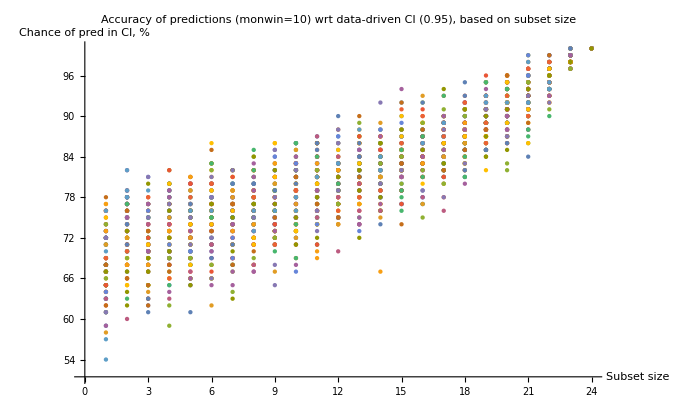

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists100, AxesLabel->{"Subset size", "Chance of pred in CI, %"}, PlotLabel->"Accuracy of predictions (monwin=10) wrt data-driven CI (0.95), based on subset size"]
```

```mathematica
(* CIs for per-subset sampling, wilson*)
 generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWilson, interWilson]
```

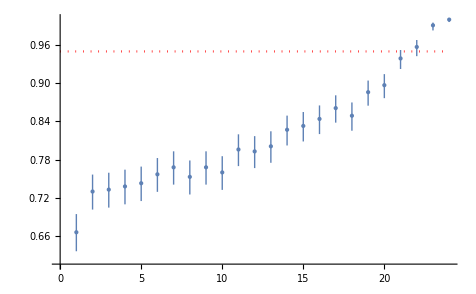

```mathematica
resestimates1000Wilson ={{1,0.6660.0300.029},{2,0.7300.0280.027},{3,0.7330.0280.026},{4,0.7380.0280.026},{5,0.7430.0280.026},{6,0.7570.0280.026},{7,0.7680.0270.025},{8,0.7530.0280.026},{9,0.7680.0270.025},{10,0.7600.0270.025},{11,0.7960.0260.024},{12,0.7930.0260.024},{13,0.8010.0260.024},{14,0.8270.0250.022},{15,0.8330.0240.022},{16,0.8440.0240.021},{17,0.8610.0230.020},{18,0.8490.0240.021},{19,0.8860.0210.018},{20,0.8970.0200.017},{21,0.9390.0170.013},{22,0.9570.0140.011},{23,0.9910.0080.004},{24,1.00000000000000000.0040.0000000000000004}};
(* clear dynamic here, despite small samples *) 
Show[ListPlot[resestimates1000Wilson, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWald, interWald]
```

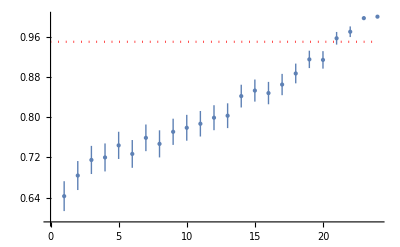

```mathematica
resestimates1000Wald = {{1,0.6430.0300.030},{2,0.6840.0290.029},{3,0.7150.0280.028},{4,0.7200.0280.028},{5,0.7440.0270.027},{6,0.7270.0280.028},{7,0.7590.0270.027},{8,0.7470.0270.027},{9,0.7710.0260.026},{10,0.7790.0260.026},{11,0.7870.0250.025},{12,0.7990.0250.025},{13,0.8030.0250.025},{14,0.8420.0230.023},{15,0.8530.0220.022},{16,0.8480.0220.022},{17,0.8650.0210.021},{18,0.8870.0200.020},{19,0.9150.0170.017},{20,0.9140.0170.017},{21,0.9570.0130.013},{22,0.9700.0110.011},{23,0.99700.00340.0034},{24,1.000000000000000001122}};
(* same dynamic here *) 
Show[ListPlot[resestimates1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
(* larger sample, wilson *)
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWilson, interWilson]
```

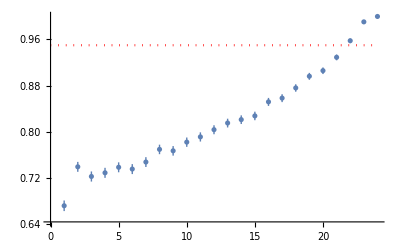

```mathematica
resestimates10000Wilson = {{1,0.6710.0090.009},{2,0.7390.0090.009},{3,0.7220.0090.009},{4,0.7280.0090.009},{5,0.7380.0090.009},{6,0.7350.0090.009},{7,0.7470.0090.008},{8,0.7690.0080.008},{9,0.7660.0080.008},{10,0.7820.0080.008},{11,0.7910.0080.008},{12,0.8030.0080.008},{13,0.8150.0080.007},{14,0.8210.0080.007},{15,0.8270.0080.007},{16,0.8520.0070.007},{17,0.8580.0070.007},{18,0.8760.0070.006},{19,0.8960.0060.006},{20,0.9060.0060.006},{21,0.9290.0050.005},{22,0.9580.0040.004},{23,0.99060.00210.0017},{24,1.000000000000000000.00040.00000000000000022}};
Show[ListPlot[resestimates10000Wilson], chart95conf]
```

```mathematica
(* larger sample, wald *)
(* redo later, maybe this was wilson *) 
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWald, interWald]
```

```mathematica
resestimates10000Wald = {{1,0.6440.0090.009},{2,0.6810.0090.009},{3,0.7030.0090.009},{4,0.7290.0090.009},{5,0.7310.0090.009},{6,0.7390.0090.009},{7,0.7560.0080.008},{8,0.7690.0080.008},{9,0.7760.0080.008},{10,0.7840.0080.008},{11,0.7900.0080.008},{12,0.8050.0080.008},{13,0.8170.0080.008},{14,0.8300.0070.007},{15,0.8470.0070.007},{16,0.8620.0070.007},{17,0.8690.0070.007},{18,0.8870.0060.006},{19,0.9030.0060.006},{20,0.9200.0050.005},{21,0.9410.0050.005},{22,0.96620.00350.0035},{23,0.99230.00170.0017},{24,1.000000000000000001122}};
Show[ListPlot[resestimates10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

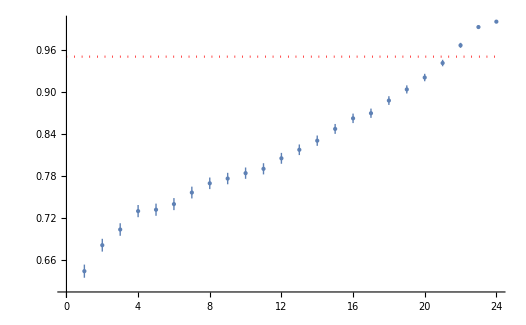

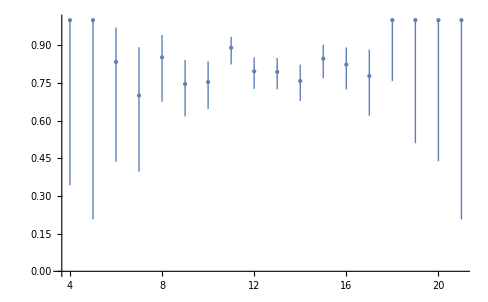

```mathematica
(* for random size sampling, WILSON: *)
(* 1000 samples, random, wilson *) 
ListPlot[generatePredvsCIOutcomes[1000], PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples, random, wilson *) 
randomOutcomes10000= generatePredvsCIOutcomes[10000]
```

{{3,0.50.40.4},{4,0.570.320.27},{5,0.890.320.09},{6,0.690.120.10},{7,0.700.090.07},{8,0.760.050.04},{9,0.7640.040.032},{10,0.7630.0270.025},{11,0.7870.0230.021},{12,0.8110.0200.019},{13,0.8130.0210.019},{14,0.8160.0220.020},{15,0.8390.0240.022},{16,0.8270.0330.029},{17,0.8510.040.034},{18,0.880.060.04},{19,0.850.130.07},{20,0.800.310.14},{21,1.000000000000000000.40.00000000000000022}}

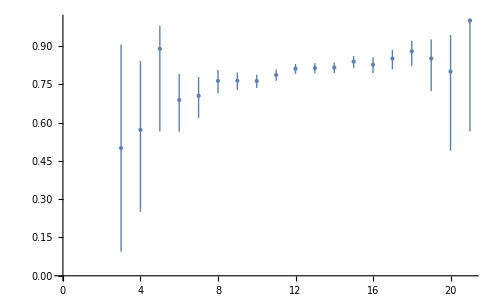

```mathematica
ListPlot[randomOutcomes10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random, wilson *) 
randomOutcomesWilson100000= generateMonFNRPredvsCIOutcomesWilson[100000]
```

{{3,0.570.320.27},{4,0.680.150.12},{5,0.710.070.06},{6,0.7470.040.035},{7,0.7300.0230.022},{8,0.7650.0150.014},{9,0.7740.0110.010},{10,0.7820.0080.008},{11,0.7920.0070.007},{12,0.7990.0060.006},{13,0.8070.0060.006},{14,0.8200.0070.006},{15,0.8370.0070.007},{16,0.8510.0090.009},{17,0.8570.0120.011},{18,0.8680.0190.017},{19,0.8720.0310.026},{20,0.910.050.04},{21,0.880.130.07},{22,1.000000000000000000.320.00000000000000022},{23,1.000000000000000000.60.00000000000000022}}

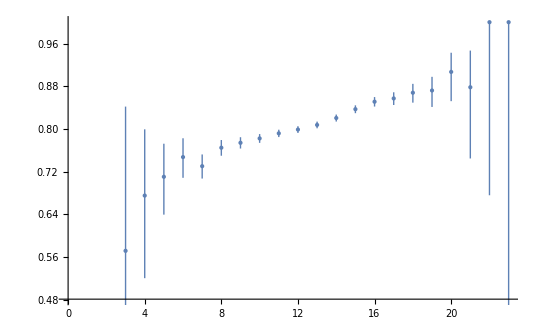

```mathematica
ListPlot[randomOutcomesWilson100000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random,  WALD *) 
generateMonFNRPredvsCIOutcomesWald[100000]
```

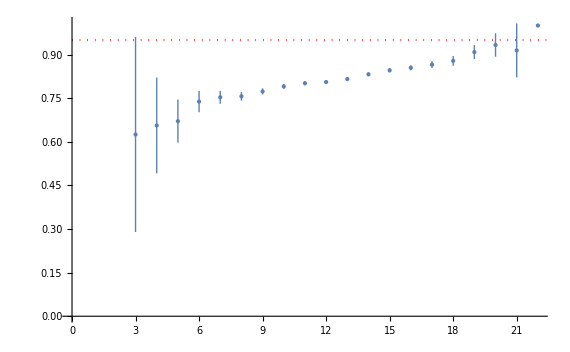

```mathematica
randomOutcomesWald100000 = {{3,0.630.340.34},{4,0.660.160.16},{5,0.670.070.07},{6,0.740.040.04},{7,0.7530.0220.022},{8,0.7560.0150.015},{9,0.7730.0110.011},{10,0.7900.0080.008},{11,0.8010.0070.007},{12,0.8060.0060.006},{13,0.8160.0060.006},{14,0.8320.0060.006},{15,0.8460.0070.007},{16,0.8540.0090.009},{17,0.8650.0120.012},{18,0.8780.0170.017},{19,0.9080.0240.024},{20,0.930.040.04},{21,0.910.090.09},{22,1.000000000000000001122}};
Show[ListPlot[randomOutcomesWald100000, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(*** THREE-WAY COMPARISON: CI, Prediction for MonFNR, and GT for MonFNR 
it is a success if we either hit the interval or both we and GT miss it 
***) 

(* returns a triple {CI interval from data, predicted FNR, GT FNR} *)
triplingMonFNRCIPredGt[pairIdList_, intervalType_] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10], (* GT of FNR *) predFNR[0.1, 10]};

(* returns false only if we missed the CI but the GT hit the CI *)
oneIntervalTripleTest[triplingFn_,pairIdList_, intervalType_] := 
With[{(*{CI,pred,GT}*) testTriple = triplingFn[pairIdList,intervalType]}, IntervalMemberQ[testTriple[[1]], testTriple[[2]]]∨¬IntervalMemberQ[testTriple[[1]], testTriple[[3]]] ];
```

```mathematica
(** THREE-WAY VISUALS FOR WILSON **) 

(* 100 samples per subset, that's not enough data *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 100, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset100 = {{1,0.870.080.05},{2,0.920.070.04},{3,0.9400.060.032},{4,0.9400.060.032},{5,0.930.070.04},{6,0.920.070.04},{7,0.870.080.05},{8,0.9500.060.028},{9,0.890.080.05},{10,0.860.080.05},{11,0.880.080.05},{12,0.870.080.05},{13,0.880.080.05},{14,0.880.080.05},{15,0.860.080.05},{16,0.900.070.04},{17,0.830.090.06},{18,0.900.070.04},{19,0.900.070.04},{20,0.930.070.04},{21,0.930.070.04},{22,0.9800.050.014},{23,1.000000000000000000.040.00000000000000022},{24,1.000000000000000000.040.00000000000000022}};
```

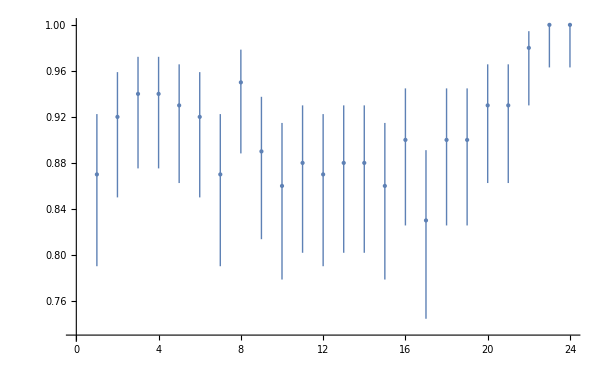

```mathematica
ListPlot[threewayPerSubset100, PlotStyle->PointSize[Large]]
```

```mathematica
(* 1k samples per subset *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000 = {{1,0.8780.0220.019},{2,0.9290.0180.014},{3,0.9190.0190.015},{4,0.9100.0190.016},{5,0.9180.0190.015},{6,0.9010.0200.017},{7,0.8760.0220.019},{8,0.8880.0210.018},{9,0.9100.0190.016},{10,0.8860.0210.018},{11,0.8890.0210.018},{12,0.8730.0220.019},{13,0.8730.0220.019},{14,0.8990.0200.017},{15,0.8840.0210.018},{16,0.9000.0200.017},{17,0.8620.0230.020},{18,0.8990.0200.017},{19,0.8990.0200.017},{20,0.9240.0180.015},{21,0.9150.0190.016},{22,0.9640.0130.010},{23,0.9920.0080.004},{24,1.00000000000000000.0040.0000000000000004}};
```

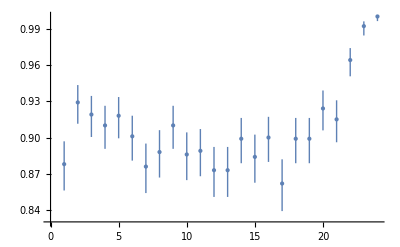

```mathematica
ListPlot[threewayPerSubset1000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples per subset *)
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWilson, interWilson, oneIntervalTripleTest]
```

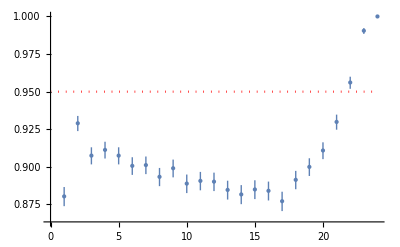

```mathematica
threewayPerSubset10000Wilson = {{1,0.8800.0070.006},{2,0.9290.0050.005},{3,0.9070.0060.006},{4,0.9110.0060.005},{5,0.9070.0060.006},{6,0.9010.0060.006},{7,0.9010.0060.006},{8,0.8930.0060.006},{9,0.8990.0060.006},{10,0.8890.0060.006},{11,0.8910.0060.006},{12,0.8900.0060.006},{13,0.8850.0060.006},{14,0.8820.0060.006},{15,0.8850.0060.006},{16,0.8840.0060.006},{17,0.8770.0070.006},{18,0.8910.0060.006},{19,0.9000.0060.006},{20,0.9110.0060.005},{21,0.9300.0050.005},{22,0.9560.0040.004},{23,0.99050.00210.0017},{24,1.000000000000000000.00040.00000000000000022}};
Show[ListPlot[threewayPerSubset10000Wilson, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(* THREE-WAY VISUALS FOR WALD *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWald, interWald, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000Wald = {{1,0.9230.0170.017},{2,0.9360.0150.015},{3,0.9200.0170.017},{4,0.9000.0190.019},{5,0.9180.0170.017},{6,0.9130.0170.017},{7,0.9010.0190.019},{8,0.9080.0180.018},{9,0.9070.0180.018},{10,0.8950.0190.019},{11,0.9000.0190.019},{12,0.8790.0200.020},{13,0.8920.0190.019},{14,0.8900.0190.019},{15,0.9070.0180.018},{16,0.8880.0200.020},{17,0.8830.0200.020},{18,0.8950.0190.019},{19,0.9150.0170.017},{20,0.9150.0170.017},{21,0.9370.0150.015},{22,0.9670.0110.011},{23,0.9900.0060.006},{24,1.000000000000000001122}};
```

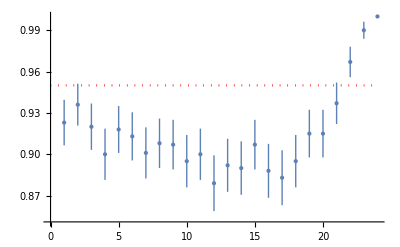

```mathematica
Show[ListPlot[threewayPerSubset1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWald, interWald, oneIntervalTripleTest]
```

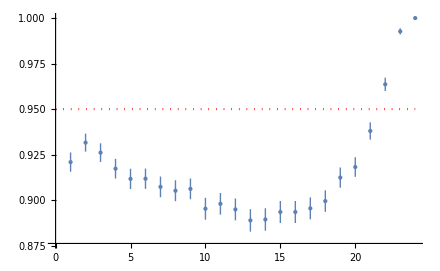

```mathematica
threewayPerSubset10000Wald = {{1,0.9210.0050.005},{2,0.9320.0050.005},{3,0.9260.0050.005},{4,0.9170.0050.005},{5,0.9120.0060.006},{6,0.9120.0060.006},{7,0.9070.0060.006},{8,0.9050.0060.006},{9,0.9060.0060.006},{10,0.8950.0060.006},{11,0.8980.0060.006},{12,0.8950.0060.006},{13,0.8890.0060.006},{14,0.8890.0060.006},{15,0.8930.0060.006},{16,0.8930.0060.006},{17,0.8960.0060.006},{18,0.8990.0060.006},{19,0.9120.0060.006},{20,0.9180.0050.005},{21,0.9380.0050.005},{22,0.9640.0040.004},{23,0.99270.00170.0017},{24,1.000000000000000001122}};
(* depressing slope, weird *) 
Show[ListPlot[threewayPerSubset10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(*** TESTING WILSON CI FOR MONITOR FNR: data-driven Wilson CI for monitor FNR vs FNR ground truth ***) 
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWilson[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWilson[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

$Aborted

```mathematica
(** VISUALS for data-driven CI vs FNR GT **)
```

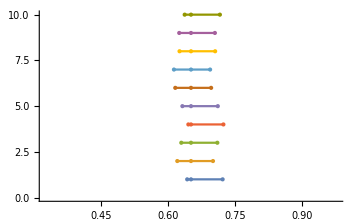

```mathematica
(* large subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},10], PlotStyle->PointSize[Large]]
```

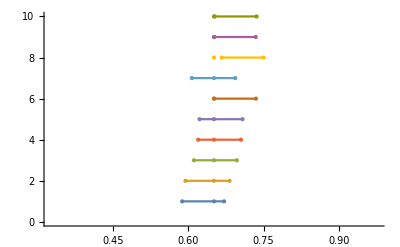

```mathematica
(* medium-large subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},10], PlotStyle->PointSize[Large]]
```

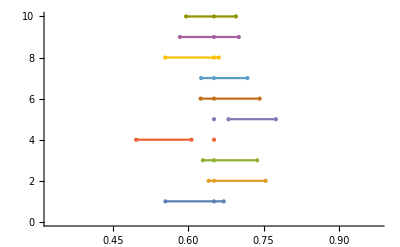

```mathematica
(* all subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},10], PlotStyle->PointSize[Large]]
```

```mathematica
(* fixed subsets CI vs mon FNR GT *) 
generateGtSuccessCountsPerSubsetSizeWilson:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWilson[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWilson, 100]
```

```mathematica
resGtLists100Wilson ={{65,58,48,45,61,55,60,57,68,62,65,67,66,65,69,70,70,69,78,78,86,86,92,98},{53,51,57,50,59,61,64,65,63,64,54,62,77,73,73,67,73,72,81,78,83,84,91,98},{53,48,48,56,62,56,56,61,62,58,57,65,75,77,70,66,72,75,78,77,84,81,90,93},{61,50,59,59,66,60,62,60,63,55,57,69,64,64,67,67,83,87,78,81,82,86,88,97},{51,52,47,57,50,61,60,59,61,63,59,67,69,70,68,71,67,79,77,87,78,80,88,98},{63,52,57,65,61,58,57,60,61,66,59,68,72,75,66,72,78,75,76,82,76,88,91,95},{63,52,59,58,60,50,63,57,69,65,65,67,68,63,70,68,79,76,76,82,85,87,92,97},{59,60,58,55,57,59,58,62,58,60,69,63,64,65,72,76,78,75,84,79,80,88,90,99},{58,63,56,64,50,57,64,56,61,71,61,62,68,75,67,71,71,77,81,88,89,85,88,98},{52,56,50,54,61,51,53,60,64,54,70,62,68,76,64,70,68,83,83,85,81,90,95,97},{55,42,53,56,60,52,59,65,53,71,62,63,73,72,73,68,73,73,84,82,85,86,84,96},{56,49,49,56,51,59,55,59,56,60,62,57,68,68,75,69,82,81,74,80,91,82,94,94},{55,63,51,62,56,62,57,65,50,65,65,63,58,68,71,69,74,78,73,79,84,87,90,94},{60,45,53,58,52,59,55,59,63,58,58,64,71,71,68,70,80,77,75,77,83,81,89,92},{55,58,54,55,61,55,52,56,59,71,73,67,66,75,70,65,78,71,73,76,84,87,83,98},{54,54,42,46,52,54,65,63,64,59,68,58,68,72,69,79,77,74,79,79,80,86,88,98},{63,47,62,56,53,59,59,55,54,67,70,69,61,74,69,76,71,79,80,88,86,87,90,92},{58,45,49,66,50,54,62,53,57,64,65,64,68,73,76,71,68,75,77,85,86,86,92,95},{60,52,58,63,55,56,61,44,54,66,60,70,62,65,66,73,80,81,80,81,87,82,88,97},{60,53,58,51,54,60,53,62,56,66,66,62,70,68,69,73,70,76,80,84,82,91,92,95},{58,54,57,59,52,58,58,64,61,66,67,61,69,74,70,72,71,78,73,85,83,87,87,95},{55,60,59,40,60,62,60,51,61,66,59,66,64,74,66,71,77,75,83,81,83,86,89,94},{68,56,54,60,57,53,63,59,54,59,63,67,59,57,71,67,65,64,78,80,83,85,84,99},{55,59,65,49,58,58,59,60,63,55,60,70,72,73,74,77,69,84,86,76,83,87,92,99},{53,63,56,45,58,53,56,64,64,55,70,71,77,76,75,73,78,74,82,85,87,86,89,95},{49,60,52,49,56,58,55,62,60,67,59,65,68,68,73,71,80,78,80,78,83,85,89,96},{51,55,48,57,58,62,57,65,56,64,62,70,69,72,71,72,75,78,80,82,81,84,90,97},{59,47,58,56,58,60,49,59,70,63,66,63,69,68,75,73,76,73,82,75,86,88,88,95},{50,56,61,62,53,55,57,60,70,58,66,68,72,73,67,73,78,84,79,78,88,78,91,93},{52,55,53,62,52,51,63,65,63,62,59,69,65,62,73,68,73,77,73,85,87,91,85,95},{52,61,50,59,59,59,52,62,62,71,63,67,64,60,75,73,81,72,89,81,87,84,88,97},{53,52,57,49,56,59,58,61,61,75,73,68,67,78,67,75,75,73,75,77,87,81,93,95},{57,55,51,53,65,65,63,55,61,74,59,62,69,66,70,69,69,75,80,88,83,89,86,96},{66,66,53,58,65,58,65,62,61,60,62,66,54,75,72,67,75,77,81,80,86,92,93,97},{63,50,54,49,54,55,63,55,55,58,69,66,65,61,69,87,69,77,80,85,81,85,94,97},{54,63,58,56,69,52,67,57,65,73,62,66,64,69,62,74,79,79,86,83,90,87,84,91},{60,54,55,57,53,57,63,52,67,69,61,62,62,67,70,74,70,73,71,81,80,90,89,98},{48,52,54,60,59,54,57,69,63,64,62,63,67,67,74,72,71,79,84,81,85,83,91,93},{46,63,51,56,53,59,59,54,62,74,61,61,67,73,69,63,74,86,76,74,79,85,92,95},{53,51,49,61,56,50,61,54,64,73,62,67,59,74,72,77,76,77,73,84,86,83,93,97},{47,61,54,60,63,53,60,59,60,65,54,66,62,72,64,77,65,72,81,81,88,83,94,96},{61,61,62,54,59,60,66,55,57,63,64,66,60,67,58,78,74,68,81,76,78,87,89,93},{59,57,54,61,54,59,55,66,65,63,67,70,72,71,68,71,76,77,73,88,85,90,91,94},{58,59,60,56,62,54,63,61,61,60,67,69,72,64,70,78,71,79,75,84,85,89,91,98},{60,51,57,58,60,65,56,66,53,65,66,57,76,66,77,69,85,68,84,85,83,81,87,97},{59,57,53,52,51,47,51,60,71,59,59,63,70,61,71,71,71,80,76,79,79,93,90,96},{46,51,60,58,52,43,58,59,60,66,72,68,67,66,70,71,75,72,84,86,85,82,90,97},{54,54,52,59,61,67,61,60,66,57,56,65,68,68,73,78,76,79,84,73,87,89,90,96},{58,55,55,50,59,63,66,64,67,60,66,65,67,70,80,81,76,77,78,78,82,86,87,97},{55,45,62,52,58,61,57,60,62,64,68,64,58,62,74,73,76,75,79,77,81,84,94,99},{63,55,46,54,52,53,59,58,62,59,55,63,61,75,70,76,73,87,76,84,88,89,89,95},{57,60,48,60,56,67,67,58,65,66,49,60,73,68,72,72,75,80,76,82,83,86,87,100},{54,47,54,61,47,59,62,65,55,60,60,63,65,63,72,69,74,74,74,82,88,90,88,100},{45,53,55,54,61,55,65,61,63,56,65,63,62,68,72,72,80,84,84,78,82,92,92,98},{57,49,45,64,55,60,61,67,57,60,65,69,70,64,76,64,73,78,87,84,76,89,92,95},{46,54,56,55,63,51,53,60,62,61,60,56,55,66,65,74,65,78,71,78,75,85,82,99},{52,49,55,62,56,51,54,53,58,58,66,55,72,72,70,75,74,75,83,81,93,83,88,96},{52,58,46,53,58,62,66,65,61,58,63,59,63,54,70,71,76,85,80,81,81,89,92,97},{64,58,54,52,53,58,59,61,57,61,67,68,65,65,64,68,69,78,77,81,86,84,94,95},{50,57,50,55,57,64,62,62,55,69,60,66,68,74,68,66,76,78,75,81,79,85,89,97},{63,55,53,59,51,46,58,60,67,65,63,66,65,71,62,72,72,74,78,87,86,90,85,98},{60,44,42,48,48,62,48,62,53,61,66,68,67,71,72,70,68,80,84,82,90,83,89,97},{58,45,58,62,48,49,60,58,56,64,59,64,62,68,65,74,69,75,74,77,84,89,93,98},{53,56,40,62,61,63,50,62,61,57,61,71,73,71,68,74,69,81,82,77,93,83,89,97},{59,46,53,53,58,58,47,58,67,66,66,61,63,63,68,72,82,84,77,86,87,89,86,96},{58,55,51,54,57,56,60,58,67,72,74,61,63,67,72,70,72,72,79,80,86,78,89,94},{57,57,51,55,54,58,61,65,66,54,57,59,80,72,71,72,73,80,72,82,87,88,90,93},{51,60,43,54,54,59,59,64,71,61,59,68,69,63,73,71,73,74,78,75,85,88,87,94},{53,58,51,52,71,64,55,61,65,54,62,61,72,64,68,71,81,74,85,80,82,87,88,95},{59,60,54,59,50,62,57,61,60,61,64,59,65,75,65,76,71,67,81,81,90,84,86,98},{55,55,54,57,52,62,59,63,64,58,57,61,72,69,68,75,80,77,83,84,86,82,94,98},{56,58,58,64,59,58,55,67,64,67,68,66,57,73,80,71,74,79,78,80,79,84,93,93},{52,60,51,46,60,64,61,66,55,67,68,64,60,75,62,78,67,79,83,84,85,88,93,94},{53,58,51,53,63,58,59,69,62,63,66,67,72,70,68,74,79,74,87,80,86,90,93,95},{56,50,58,58,46,59,60,65,48,63,64,63,58,68,68,72,70,84,80,83,81,81,87,97},{58,56,66,47,52,57,55,62,58,63,65,67,62,65,77,65,68,82,82,84,86,83,89,98},{56,52,66,51,60,61,52,65,60,66,63,64,69,70,66,72,82,74,76,80,88,86,92,97},{53,46,59,49,55,63,58,66,60,55,68,66,63,79,78,75,75,75,82,84,84,87,90,98},{59,56,57,50,56,61,63,52,67,66,67,64,68,65,72,78,81,71,78,83,90,84,86,91},{53,53,55,51,57,50,58,61,61,56,68,67,66,73,78,76,72,79,80,75,81,84,93,98},{56,56,48,56,60,59,52,55,63,58,56,63,74,63,73,69,79,81,71,79,85,83,88,96},{56,47,62,53,60,56,60,60,61,66,67,66,74,73,65,74,75,77,74,82,84,84,86,99},{53,56,49,56,60,62,52,60,61,60,54,71,66,75,67,82,75,78,79,86,82,89,88,98},{62,53,66,58,59,54,55,52,56,54,61,63,71,70,72,63,79,78,78,87,77,87,88,92},{54,54,55,58,43,61,59,60,59,62,56,75,63,64,65,72,74,78,82,80,88,91,85,94},{59,52,53,57,65,54,61,62,61,65,59,60,65,70,69,73,70,78,84,82,88,88,92,97},{54,49,54,62,48,54,64,63,51,59,72,68,68,79,74,71,75,82,77,82,89,88,91,89},{51,58,52,62,59,50,59,63,54,66,66,60,74,67,73,70,70,74,77,78,81,94,95,97},{52,63,58,54,57,62,58,55,56,64,61,66,66,63,73,75,78,81,78,78,82,87,88,96},{55,58,58,61,56,48,55,61,61,66,69,69,66,76,71,69,75,71,83,76,79,84,87,94},{55,50,62,59,61,55,58,58,73,64,68,66,68,72,71,70,79,73,71,81,80,82,85,95},{55,46,53,67,49,62,64,66,63,56,59,65,69,62,68,78,77,75,83,85,87,86,85,99},{53,51,57,53,60,58,58,62,63,61,58,64,62,76,73,76,75,72,80,85,76,92,86,94},{56,60,59,46,56,54,55,55,58,52,68,64,68,66,75,67,78,77,78,87,88,90,94,93},{62,49,57,49,54,60,61,56,68,66,65,67,66,71,59,71,71,77,78,74,83,88,83,99},{63,55,59,49,62,57,60,57,63,67,61,77,73,63,70,80,86,74,77,79,80,87,93,93},{52,54,44,61,56,62,66,64,69,64,59,71,61,79,81,79,66,82,78,85,83,90,91,97},{57,56,49,59,56,57,61,58,61,65,68,55,72,74,72,68,76,71,78,80,86,87,85,94},{56,59,54,59,55,59,67,72,63,62,68,64,59,73,73,75,73,72,79,82,85,80,89,98},{48,52,54,54,52,58,68,59,66,68,70,64,65,64,68,72,73,83,82,84,86,86,86,94}}
```

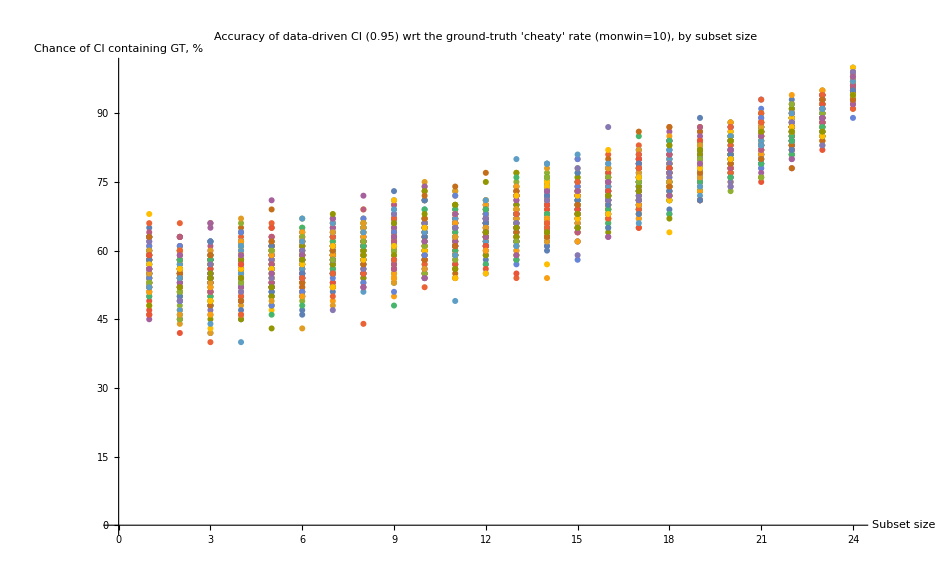

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resGtLists100Wilson, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
(*** TESTING WALD CI FOR MONITOR FNR GT ***)
```

```mathematica
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWald[pairIdList_] := IntervalMemberQ[(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWald[pairIdList_] := {(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

```mathematica
generateGtSuccessCountsPerSubsetSizeWald:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWald[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWald, 100]
```

```mathematica
resListsWald100a = {{54,46,57,59,55,54,60,54,66,69,61,70,76,65,70,67,74,73,79,80,70,80,88,90},{60,56,46,55,52,53,51,64,64,61,73,68,70,66,67,77,71,74,76,82,81,82,89,99},{53,58,52,50,56,55,70,62,61,60,56,60,62,75,72,77,69,73,69,75,77,81,84,99},{52,60,52,66,50,56,59,61,64,62,71,63,60,65,63,73,72,70,78,78,81,80,92,96},{49,49,55,53,57,58,61,56,51,65,60,58,65,66,67,68,67,78,78,79,85,86,87,98},{43,55,53,55,58,60,61,56,57,64,64,65,58,65,67,75,68,77,73,75,88,89,86,97},{47,53,55,57,55,52,57,56,57,55,65,64,59,69,72,67,76,77,81,86,83,87,87,96},{51,54,52,46,54,55,66,57,63,62,58,62,71,75,65,76,65,78,82,83,77,88,90,97},{50,52,52,50,58,55,62,60,59,54,73,68,63,74,71,66,79,75,79,77,83,88,95,95},{57,51,51,50,58,64,56,55,55,54,67,60,61,69,75,77,68,84,74,80,77,85,86,97},{52,50,53,53,51,62,55,56,71,63,65,73,65,67,69,66,69,75,81,79,83,90,88,99},{57,55,45,51,59,50,51,62,54,58,60,58,65,61,70,70,69,71,73,79,70,88,88,98},{52,52,58,67,53,54,51,57,62,64,62,67,71,63,62,72,83,85,72,77,89,90,84,98},{56,50,54,51,56,55,52,65,50,71,59,66,68,67,66,72,74,82,74,74,83,81,91,95},{50,52,48,45,54,58,65,59,60,67,71,69,65,64,79,75,71,78,90,87,90,86,89,96},{54,57,55,56,60,60,49,57,66,59,64,73,70,70,70,83,76,80,78,83,79,86,90,97},{49,55,49,56,54,53,60,58,59,60,63,66,68,64,71,72,75,75,77,76,86,83,91,96},{55,47,56,48,46,61,57,61,61,65,65,62,67,69,67,70,75,72,77,79,86,86,87,96},{50,47,51,50,53,43,68,56,63,59,66,68,57,67,73,74,72,85,79,73,76,83,87,99},{46,46,56,47,53,53,62,53,58,65,68,56,63,65,75,70,76,72,80,77,87,86,85,97},{57,56,48,53,49,66,60,62,67,63,63,71,71,67,67,72,66,75,77,79,78,81,91,95},{52,55,48,51,60,55,51,60,66,56,73,73,61,72,71,70,72,81,66,88,73,84,87,97},{45,54,55,52,56,63,56,59,68,65,65,74,67,63,75,76,70,72,69,80,81,91,87,98},{56,51,46,61,62,51,56,58,62,59,62,59,66,71,70,72,76,76,77,81,85,85,93,97},{51,56,55,48,50,48,57,54,52,61,68,59,77,69,63,72,72,71,82,77,80,83,85,97},{56,53,54,54,56,55,48,60,59,63,70,64,70,70,63,75,80,74,74,78,80,84,89,96},{51,52,42,47,44,55,63,60,58,63,68,63,61,70,75,64,78,74,79,76,83,79,88,96},{45,53,49,62,51,54,51,61,64,56,61,65,62,64,61,72,86,79,76,83,80,85,90,98},{50,49,44,50,54,55,55,48,59,55,63,68,68,76,70,70,76,82,78,81,84,84,89,100},{50,56,52,60,56,67,60,58,69,56,59,74,75,66,71,72,77,75,78,82,86,81,89,96},{41,47,48,48,64,57,57,58,61,66,52,63,66,62,74,79,74,67,72,84,85,86,86,95},{48,57,53,56,50,57,69,57,64,63,62,63,70,58,75,74,64,70,78,79,83,86,90,95},{57,55,53,55,51,59,63,66,66,74,58,64,70,65,77,74,78,75,79,85,77,81,83,97},{56,54,52,55,48,52,60,57,61,67,61,72,64,67,62,69,69,80,76,84,74,76,86,91},{49,52,57,52,49,53,59,61,55,69,66,60,63,70,73,67,81,75,75,83,80,84,89,96},{53,53,45,58,53,63,50,59,66,65,62,78,69,67,67,71,76,72,82,83,84,79,88,97},{65,44,55,55,56,64,59,53,55,57,65,61,64,65,73,76,78,78,78,74,82,86,85,95},{53,52,52,49,48,62,65,60,69,59,60,64,75,68,63,66,69,75,75,83,84,81,92,95},{51,48,50,58,52,53,54,62,62,58,63,66,71,60,59,73,73,79,88,78,86,85,90,94},{54,57,59,52,55,64,55,56,58,69,65,60,71,69,73,73,74,71,80,77,74,77,84,99},{54,47,57,61,51,55,61,50,62,61,59,64,73,77,68,70,70,76,80,78,80,86,90,100},{52,51,48,57,57,67,56,60,59,63,63,61,73,64,77,81,73,76,80,78,81,87,91,97},{51,62,49,56,57,55,58,69,69,64,55,60,65,66,69,66,73,72,82,75,81,88,80,95},{54,52,54,49,52,62,51,54,59,61,57,59,71,72,71,65,73,79,81,83,81,84,90,96},{53,46,48,55,62,56,51,56,48,62,61,66,66,67,70,79,69,72,74,85,78,87,84,94},{53,54,52,53,59,63,63,58,62,59,67,62,69,71,67,71,83,80,85,78,80,77,87,95},{52,49,52,58,61,54,58,57,69,59,58,60,61,72,68,69,78,77,80,82,85,78,85,95},{56,50,52,54,54,54,55,51,57,69,58,64,66,69,72,67,76,77,75,83,83,81,86,98},{54,45,42,57,54,49,55,62,65,58,56,68,65,66,71,78,71,79,73,82,85,84,90,96},{56,53,54,56,55,62,59,68,66,69,70,65,66,66,75,71,72,72,73,82,86,87,89,96},{42,47,52,57,63,54,56,61,58,60,62,64,63,65,73,66,75,75,75,78,74,85,89,95},{47,57,53,50,52,55,57,60,58,56,68,66,67,65,63,62,70,79,74,77,80,91,90,97},{53,45,55,61,53,60,56,59,60,60,61,76,51,68,68,78,70,70,81,86,78,86,86,97},{57,49,50,49,54,59,57,56,60,61,60,55,69,63,74,75,71,77,78,77,86,83,86,95},{60,52,55,52,58,53,62,63,57,65,57,68,73,69,79,72,75,80,70,78,90,87,87,98},{58,47,46,50,57,55,48,57,59,61,66,66,63,78,78,67,75,80,80,84,82,90,89,95},{51,42,60,53,51,59,65,58,71,65,56,67,65,64,66,75,66,68,77,87,76,87,85,94},{52,59,57,41,55,55,55,58,61,61,67,64,68,68,70,68,82,72,82,77,81,84,91,98},{43,58,56,45,56,55,62,65,63,68,70,65,72,67,60,75,68,80,79,80,87,90,91,95},{46,51,61,55,47,67,58,59,64,67,56,62,74,68,61,74,64,76,79,81,79,84,88,100},{55,60,63,47,54,58,49,62,62,57,64,64,59,62,74,76,76,74,80,76,75,82,91,97},{50,47,54,58,55,46,55,61,60,62,67,59,64,68,78,65,74,77,84,85,84,92,94,97},{54,58,48,54,56,55,48,51,66,71,58,67,68,68,65,65,67,82,77,77,78,84,88,99},{56,45,52,56,54,58,61,61,54,62,68,65,75,69,76,66,70,75,80,77,84,84,87,97},{51,58,61,51,56,52,58,63,63,68,64,61,66,68,70,77,73,75,77,75,82,82,89,99},{50,51,60,63,51,55,69,58,56,61,55,64,64,69,64,70,80,76,74,71,82,80,86,93},{56,47,49,47,56,49,52,55,53,58,63,66,63,66,74,68,75,80,78,73,80,86,87,94},{41,53,48,44,53,55,57,57,60,58,70,66,66,55,78,71,70,81,81,77,81,89,92,97},{52,50,55,57,58,58,53,70,61,65,59,63,69,68,67,79,69,73,75,77,81,89,91,96},{44,57,45,50,55,56,61,58,55,55,63,68,66,71,67,68,79,78,84,82,78,87,90,100},{51,52,55,57,56,52,60,63,51,61,63,69,69,68,64,65,78,75,84,78,83,86,92,96},{61,52,49,49,60,56,61,65,64,66,63,65,74,70,66,72,71,73,77,77,81,87,90,95},{61,55,50,53,56,67,53,68,70,61,67,64,59,72,68,70,78,73,81,82,85,87,93,98},{45,53,66,61,56,54,66,58,65,61,58,62,60,69,79,72,73,71,82,80,84,83,87,96},{53,59,50,52,62,55,58,69,67,62,62,64,68,59,63,66,70,76,77,87,87,83,89,99},{54,48,47,58,47,58,62,58,54,61,67,69,62,60,74,73,77,73,78,78,83,88,91,98},{51,52,55,45,56,53,54,60,69,67,62,72,63,65,63,76,80,74,78,76,87,92,84,97},{58,59,53,59,52,59,50,53,66,59,69,66,63,76,70,77,71,76,81,75,85,87,80,95},{48,52,58,55,59,55,62,61,62,70,69,62,68,67,73,64,78,80,76,62,83,83,86,100},{45,44,52,55,48,53,58,53,57,68,59,64,67,72,69,59,79,81,84,78,88,83,85,96},{55,47,50,55,56,58,60,58,63,68,71,65,70,56,71,75,81,80,72,79,79,82,90,95},{59,48,60,57,53,53,51,64,64,65,71,66,63,67,66,74,75,76,77,78,82,81,85,96},{56,49,42,49,45,60,60,49,53,58,67,61,67,68,73,75,65,73,73,79,80,87,95,96},{53,47,51,55,54,59,61,54,51,65,65,65,67,73,70,71,68,75,78,78,77,81,90,98},{58,51,42,44,61,61,58,58,62,68,66,71,62,67,73,69,72,78,71,79,86,79,89,93},{59,46,51,49,54,67,54,57,50,61,70,62,61,64,67,64,81,83,71,79,83,91,85,95},{53,52,51,55,55,48,59,69,59,71,68,63,68,69,68,69,82,77,78,85,82,82,89,94},{54,54,57,58,59,53,58,67,60,75,71,63,60,74,68,74,80,74,72,77,80,86,83,96},{57,57,64,53,61,58,56,54,68,64,71,65,62,66,74,74,78,69,84,92,86,85,82,95},{48,45,61,46,61,61,58,58,56,65,62,60,67,74,77,74,75,75,82,83,87,85,84,96},{56,47,57,60,52,59,55,58,56,62,61,62,58,74,67,65,71,84,79,82,86,84,78,97},{46,47,55,57,64,56,60,61,45,59,68,53,64,67,68,66,78,78,70,81,84,83,92,95},{48,54,57,57,56,60,49,54,60,63,68,73,65,65,67,76,68,80,78,78,78,88,89,95},{47,45,48,45,54,62,59,62,61,64,65,63,62,59,69,75,75,80,74,84,75,88,87,96},{53,47,51,52,61,59,66,59,57,65,69,63,72,69,69,72,78,72,76,86,78,86,88,95},{45,55,51,45,48,60,56,45,62,67,60,68,76,74,79,80,67,79,77,83,82,80,91,96},{51,53,59,56,53,55,53,55,65,71,62,67,71,63,72,74,81,78,78,77,75,77,89,96},{46,57,57,61,51,58,61,60,68,58,57,62,61,70,68,74,72,80,76,79,80,84,89,94},{55,51,54,57,53,53,60,55,58,66,68,71,66,75,61,65,83,78,70,76,78,78,90,96},{44,49,59,58,53,59,60,58,60,60,53,69,67,72,69,66,70,87,82,83,78,83,84,94}};
```

```mathematica
(* ANOTHER 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWald, 100]
```

```mathematica
resListsWald100b = {{38,57,53,49,48,58,63,59,53,60,60,54,66,71,67,66,61,67,85,68,80,80,88,99},{59,47,49,56,54,50,62,57,61,66,70,63,66,78,71,72,70,78,80,80,84,84,84,95},{43,54,53,58,57,45,51,69,62,66,63,73,66,60,67,66,70,80,81,77,83,86,88,93},{47,50,58,46,50,59,60,61,59,65,61,62,69,73,63,71,74,78,73,85,86,89,91,99},{47,49,58,59,46,46,57,56,60,69,72,59,71,71,75,68,69,78,76,84,78,82,89,97},{51,49,52,55,56,44,53,61,68,63,71,71,69,64,61,73,72,71,78,85,87,89,91,95},{49,46,58,53,50,55,60,63,60,68,60,53,66,65,71,66,71,81,70,87,84,85,84,96},{54,54,43,59,56,49,56,56,67,61,71,68,69,72,73,67,80,78,74,86,86,88,88,98},{48,45,51,47,52,52,56,59,55,63,69,68,65,67,76,78,73,79,79,78,81,81,91,97},{50,46,44,50,49,61,53,64,59,68,66,62,52,74,70,64,74,68,65,76,85,87,81,94},{47,52,61,52,56,56,64,62,58,57,50,61,66,64,75,67,78,74,82,82,81,84,86,93},{46,52,45,54,56,57,66,62,54,59,64,56,75,68,69,79,70,76,78,79,90,86,93,98},{57,44,57,58,48,61,52,56,62,64,67,65,64,70,72,70,76,76,80,78,82,76,90,96},{53,47,51,63,53,57,61,55,66,66,68,60,68,65,72,69,74,72,81,78,87,87,86,93},{46,62,59,51,57,62,62,57,63,66,52,64,66,69,65,73,78,66,84,80,82,87,88,99},{45,45,58,49,51,60,66,58,66,60,69,66,67,64,66,74,65,76,79,84,85,86,87,95},{55,46,56,52,48,55,58,63,64,61,68,65,59,67,69,64,80,80,73,78,81,91,92,97},{54,50,47,56,60,50,55,61,56,58,59,65,63,70,76,67,65,71,78,85,80,77,89,92},{50,51,61,53,59,51,56,62,57,61,69,65,64,63,68,70,67,82,77,83,80,84,90,93},{48,59,56,58,55,60,65,58,64,60,61,69,74,67,71,72,70,74,78,78,77,83,88,98},{52,43,51,55,59,57,64,50,69,61,68,69,57,69,73,79,75,82,77,81,90,85,86,94},{53,46,57,65,52,55,65,61,66,67,62,66,61,61,62,74,75,81,81,82,80,86,89,96},{43,43,58,51,60,55,58,50,66,64,61,63,75,69,78,62,78,72,81,75,82,84,86,99},{52,51,43,51,59,54,61,47,69,65,70,67,63,61,68,65,76,79,67,80,77,83,95,95},{52,49,54,60,51,56,57,65,55,64,67,66,67,71,76,72,75,80,79,82,80,83,87,99},{55,56,54,49,59,50,64,54,58,63,65,66,66,71,76,66,79,76,78,80,84,86,88,97},{52,48,46,57,56,57,55,63,62,66,69,68,60,63,62,75,74,71,74,84,81,88,85,96},{47,52,51,61,56,55,57,62,57,55,64,60,78,69,76,68,76,79,83,83,78,83,87,97},{47,59,52,53,41,62,63,65,56,53,65,65,74,72,76,69,78,74,74,79,84,86,93,96},{48,53,46,56,55,54,51,68,67,63,64,66,74,64,58,67,69,75,76,79,80,87,92,99},{49,57,60,58,52,51,59,59,64,61,62,73,63,64,65,75,75,78,76,83,82,84,85,96},{51,45,53,43,57,48,58,57,58,59,63,58,69,75,60,78,75,84,68,74,85,82,90,97},{48,53,50,67,56,47,62,52,60,58,62,67,73,69,68,72,76,79,75,77,79,84,87,98},{51,54,58,50,56,54,53,58,61,63,57,61,65,69,81,80,69,77,79,81,79,91,85,97},{53,46,58,54,50,60,66,53,64,60,64,61,65,76,66,69,72,75,76,74,78,79,90,95},{56,45,48,55,56,61,53,69,65,65,60,64,75,73,72,68,70,66,85,84,84,90,89,99},{52,52,57,55,59,43,54,61,61,58,65,69,70,74,66,75,68,78,72,83,75,88,88,95},{55,46,55,54,53,58,59,57,66,64,62,78,60,77,65,75,84,77,70,77,80,82,84,95},{55,55,52,57,54,56,47,62,57,73,69,68,65,79,69,70,79,76,80,82,77,86,87,92},{51,55,51,50,52,59,59,62,60,58,64,56,64,68,64,73,80,73,75,79,86,86,97,96},{56,57,53,49,55,53,54,51,56,60,58,64,71,68,66,70,72,74,74,79,84,80,93,95},{54,53,61,47,62,57,59,62,62,60,60,59,65,75,65,66,67,73,79,86,80,85,86,96},{52,55,50,60,53,55,47,60,67,66,66,66,53,64,75,66,78,78,74,82,80,85,82,96},{54,64,50,52,59,62,62,55,60,65,62,71,69,66,68,78,76,74,86,76,82,83,88,96},{54,55,50,63,46,57,62,57,61,57,66,62,65,66,78,64,68,74,72,74,83,85,84,99},{52,49,43,53,61,57,56,59,59,62,63,69,63,66,66,80,70,76,81,74,83,84,90,95},{38,46,59,50,54,61,57,63,54,63,68,68,65,67,70,75,77,69,74,76,82,82,94,99},{51,56,65,63,62,59,55,70,58,61,61,62,73,68,76,73,73,79,80,74,75,88,88,94},{55,59,50,48,64,48,58,55,59,57,66,71,66,65,65,70,77,79,73,74,84,80,88,97},{53,51,55,57,55,55,50,61,58,65,55,69,71,68,68,77,70,70,79,82,75,89,88,96},{57,48,51,65,58,61,62,55,52,57,59,72,69,74,72,80,72,75,73,83,85,82,92,96},{58,41,65,48,53,54,52,61,57,63,60,71,62,71,73,76,68,82,79,83,88,84,85,99},{55,52,58,54,54,62,52,63,60,61,64,63,69,61,65,71,80,78,85,79,81,87,87,95},{46,56,56,60,54,54,54,67,57,61,60,62,68,74,65,74,77,65,78,76,82,80,89,95},{55,50,47,64,60,60,45,56,59,68,61,59,65,66,68,72,86,74,78,80,80,88,84,96},{50,48,53,56,68,66,56,58,57,63,63,65,62,71,70,76,74,74,83,82,82,85,86,97},{61,44,47,58,59,48,59,59,54,66,67,62,69,62,70,67,79,79,79,71,85,84,87,97},{49,55,55,56,56,63,60,58,57,65,66,63,63,70,64,71,68,75,87,72,82,86,84,96},{64,42,50,58,47,53,57,58,64,61,62,64,69,66,64,68,77,71,74,80,92,85,89,94},{53,52,50,58,50,63,57,57,67,68,59,67,66,65,69,72,69,80,76,83,81,82,87,94},{53,48,53,54,61,46,59,55,60,62,62,61,58,65,75,70,75,83,76,85,79,91,91,98},{45,47,46,47,55,61,54,58,66,67,68,68,67,63,72,68,71,71,77,78,83,93,86,97},{57,52,61,56,59,62,58,69,67,62,65,64,69,73,67,65,65,72,77,79,86,90,90,94},{47,47,52,59,56,62,66,57,55,57,73,65,66,69,62,61,73,71,75,86,84,88,93,99},{45,52,63,57,56,53,67,64,63,67,58,72,65,68,71,72,67,69,76,81,83,82,86,98},{47,43,53,50,55,62,63,58,57,50,67,65,60,68,69,69,77,83,78,72,84,82,85,97},{58,48,57,55,59,52,63,44,67,52,67,60,66,64,63,64,80,75,81,85,84,87,90,94},{55,54,41,57,45,59,61,59,65,65,69,66,64,62,65,76,78,74,74,84,78,83,89,97},{45,48,53,55,54,58,58,59,64,60,70,66,57,64,63,71,72,81,79,85,81,89,87,97},{49,56,55,58,49,52,66,56,54,58,63,62,66,61,73,68,71,79,76,81,75,79,87,98},{45,53,55,59,49,63,58,62,69,60,61,65,68,71,74,71,77,72,76,81,84,91,86,96},{45,48,55,53,45,62,64,56,62,52,66,68,65,71,72,68,73,74,71,80,76,90,85,99},{54,48,52,47,60,55,62,58,62,57,61,71,63,77,69,65,71,74,77,78,80,90,87,94},{51,55,50,58,51,58,61,59,58,65,63,59,68,71,75,74,77,81,78,80,86,84,88,93},{47,54,54,45,53,63,59,52,63,64,63,66,66,66,65,76,76,78,76,80,77,77,88,96},{56,42,58,53,57,51,62,57,54,63,63,59,56,65,67,69,71,78,80,76,79,84,91,97},{56,62,48,60,56,52,61,64,53,64,62,61,63,68,82,79,74,71,81,82,87,88,85,97},{61,46,52,40,56,58,52,59,63,61,67,67,73,69,72,73,73,79,78,82,88,88,86,99},{56,52,61,53,57,55,55,61,64,61,56,72,75,72,74,71,82,81,75,82,83,86,84,97},{50,50,51,58,49,53,57,58,57,68,62,73,65,67,72,71,75,75,74,81,84,84,85,92},{52,50,48,59,43,55,59,66,52,59,60,69,61,64,71,71,78,80,79,80,86,85,86,95},{56,59,54,54,68,63,54,55,64,67,57,59,60,65,69,66,77,76,84,86,86,90,88,95},{51,46,51,52,64,44,55,63,61,69,57,56,65,64,65,80,69,79,80,83,86,91,90,97},{57,48,48,49,65,64,53,60,65,65,65,55,72,68,77,70,79,76,75,77,77,84,88,93},{58,56,48,56,53,62,63,57,51,63,64,67,64,71,69,76,70,78,71,72,86,73,87,95},{50,66,50,53,52,57,74,63,60,58,63,73,70,71,68,71,76,74,81,75,74,84,88,97},{53,49,55,45,50,59,49,54,64,52,64,70,70,65,68,70,69,75,76,84,79,81,89,97},{55,52,55,59,54,62,58,63,46,63,61,64,68,72,69,72,78,77,81,83,85,82,83,98},{54,53,52,63,55,54,55,64,62,63,60,76,69,70,71,72,77,71,81,76,82,86,88,93},{55,52,60,52,56,46,55,65,62,62,58,68,64,72,73,72,80,79,78,77,83,81,88,94},{53,40,44,47,48,58,55,63,53,69,62,67,69,56,71,75,70,69,80,80,91,90,89,95},{56,49,46,58,53,57,59,62,66,67,62,61,66,68,71,75,71,77,84,79,83,82,81,98},{55,49,52,60,50,55,62,57,61,60,62,62,65,75,67,74,79,71,73,85,81,86,88,98},{41,47,50,53,54,66,56,62,57,54,63,62,65,73,69,73,77,74,75,86,83,85,83,95},{47,57,51,49,54,53,56,58,58,68,68,76,64,69,72,66,64,70,81,78,78,87,88,97},{46,52,48,62,51,61,51,59,59,64,69,62,63,64,73,74,73,82,72,81,89,81,90,97},{48,47,52,58,59,54,60,61,60,64,69,69,58,64,71,71,74,72,79,73,79,90,86,95},{53,52,53,60,63,68,58,59,58,64,74,73,68,69,66,75,68,70,80,84,76,86,87,94},{50,46,58,50,53,49,62,57,62,55,65,69,60,66,67,73,75,77,74,78,80,82,88,92},{52,47,48,54,58,45,60,62,57,61,62,71,63,66,68,67,70,77,76,83,76,90,91,97}};
```

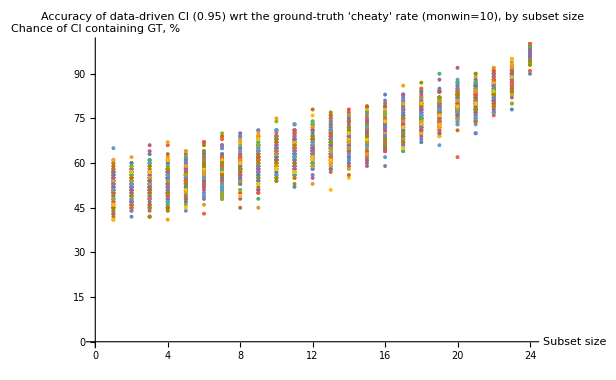

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100a, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100b, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

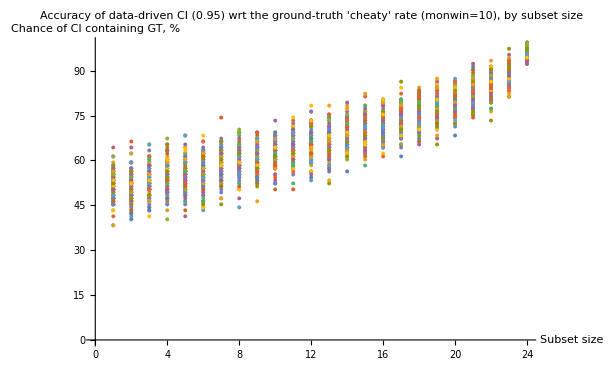

```mathematica
(** randomized sampling for wald CI vs ground truth monitor FNR **)
```

```mathematica
(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generateMonGtFNRvsCISample[sampleCt_]:= ({#[[1]],oneIntervalGtTestWald[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));


(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on wilson CIs} *) 
generateMonGtFNRvsCIOutcomesWald[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWald[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpPredvsCISample[generateMonGtFNRvsCISample[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

```mathematica
(* 10k samples randomly *)
generateMonGtFNRvsCIOutcomesWald[10000]
```

```mathematica
randomOutcomesMonFNRGtWald10000 = {{5,0.450.220.22},{6,0.400.130.13},{7,0.550.080.08},{8,0.590.050.05},{9,0.570.040.04},{10,0.6010.0300.030},{11,0.6260.0270.027},{12,0.6360.0240.024},{13,0.6760.0230.023},{14,0.6820.0250.025},{15,0.6960.0290.029},{16,0.7360.0350.035},{17,0.780.040.04},{18,0.730.080.08},{19,0.800.110.11},{20,1.000000000000000001122},{21,0.70.50.5}};
```

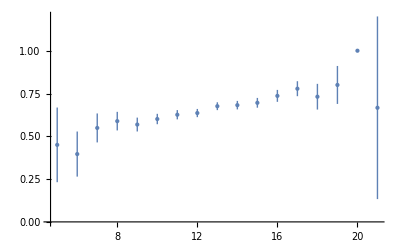

```mathematica
ListPlot[randomOutcomesMonFNRGtWald10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples randomly *) 
generateMonGtFNRvsCIOutcomesWald[100000]
```

```mathematica
randomOutcomesMonFNRGtWald100000 ={{3,0.200.200.35},{4,0.440.160.16},{5,0.480.080.08},{6,0.580.040.04},{7,0.5830.0250.025},{8,0.5970.0170.017},{9,0.5960.0120.012},{10,0.6150.0100.010},{11,0.6330.0080.008},{12,0.6500.0070.007},{13,0.6680.0070.007},{14,0.6810.0080.008},{15,0.6980.0090.009},{16,0.7170.0110.011},{17,0.7470.0150.015},{18,0.7740.0210.021},{19,0.760.040.04},{20,0.800.060.06},{21,0.870.100.10},{22,1.000000000000000001122},{23,1.000000000000000001122}};
```

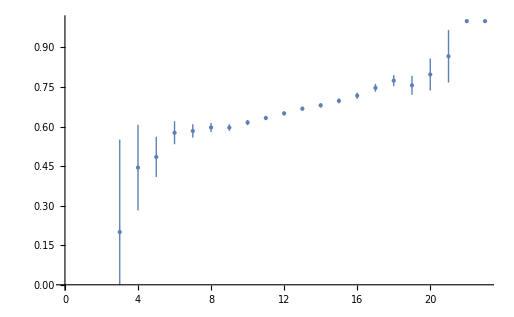

```mathematica
ListPlot[randomOutcomesMonFNRGtWald100000, PlotStyle->PointSize[Large]]
```